```mathematica
w1=1;
w2=2;
w3=1;
w4=1;
w5=1;
w6=1;
w7=1;
w8=1;
k=10000;
n=8;
io1=2Pi*RandomReal[];
io2=2Pi*RandomReal[];
io3=2Pi*RandomReal[];
io4=2Pi*RandomReal[];
io5=2Pi*RandomReal[];
io6=2Pi*RandomReal[];
io7=2Pi*RandomReal[];
io8=2Pi*RandomReal[];
```

```mathematica
res=NDSolve[{
o1'[t]==w1-k/n(Sin[o1[t]-o2[t]]+Sin[o1[t]-o3[t]]+Sin[o1[t]-o4[t]]+Sin[o1[t]-o5[t]]+Sin[o1[t]-o6[t]]+Sin[o1[t]-o7[t]]+Sin[o1[t]-o8[t]]),
o2'[t]==w2-k/n(Sin[o2[t]-o1[t]]+Sin[o2[t]-o3[t]]+Sin[o2[t]-o4[t]]+Sin[o2[t]-o5[t]]+Sin[o2[t]-o6[t]]+Sin[o2[t]-o7[t]]+Sin[o2[t]-o8[t]]),
o3'[t]==w3-k/n(Sin[o3[t]-o1[t]]+Sin[o3[t]-o2[t]]+Sin[o3[t]-o4[t]]+Sin[o3[t]-o5[t]]+Sin[o3[t]-o6[t]]+Sin[o3[t]-o7[t]]+Sin[o3[t]-o8[t]]),
o4'[t]==w4-k/n(Sin[o4[t]-o1[t]]+Sin[o4[t]-o2[t]]+Sin[o4[t]-o3[t]]+Sin[o4[t]-o5[t]]+Sin[o4[t]-o6[t]]+Sin[o4[t]-o7[t]]+Sin[o4[t]-o8[t]]),
o5'[t]==w5-k/n(Sin[o5[t]-o1[t]]+Sin[o5[t]-o2[t]]+Sin[o5[t]-o3[t]]+Sin[o5[t]-o4[t]]+Sin[o5[t]-o6[t]]+Sin[o5[t]-o7[t]]+Sin[o5[t]-o8[t]]),
o6'[t]==w6-k/n(Sin[o6[t]-o1[t]]+Sin[o6[t]-o2[t]]+Sin[o6[t]-o3[t]]+Sin[o6[t]-o4[t]]+Sin[o6[t]-o5[t]]+Sin[o6[t]-o7[t]]+Sin[o6[t]-o8[t]]),
o7'[t]==w7-k/n(Sin[o7[t]-o1[t]]+Sin[o7[t]-o2[t]]+Sin[o7[t]-o3[t]]+Sin[o7[t]-o4[t]]+Sin[o7[t]-o5[t]]+Sin[o7[t]-o6[t]]+Sin[o7[t]-o8[t]]),
o8'[t]==w8-k/n(Sin[o8[t]-o1[t]]+Sin[o8[t]-o2[t]]+Sin[o8[t]-o3[t]]+Sin[o8[t]-o4[t]]+Sin[o8[t]-o5[t]]+Sin[o8[t]-o6[t]]+Sin[o8[t]-o7[t]]),
o1[0]==io1,
o2[0]==io2,
o3[0]==io3,
o4[0]==io4,
o5[0]==io5,
o6[0]==io6,
o7[0]==io7,
o8[0]==io8
},{o1,o2,o3,o4,o5,o6,o7,o8},{t,0,100}];
```

```mathematica
oo1=o1/.res[[1]];
oo2=o2/.res[[1]];
oo3=o3/.res[[1]];
oo4=o4/.res[[1]];
oo5=o5/.res[[1]];
oo6=o6/.res[[1]];
oo7=o7/.res[[1]];
oo8=o8/.res[[1]];
```

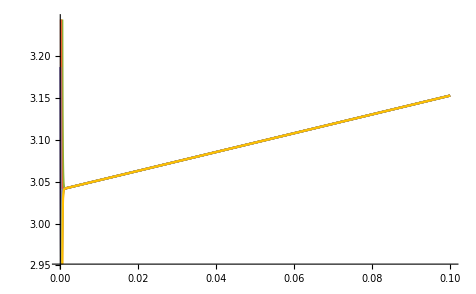

```mathematica
Plot[{oo1[t],oo2[t],oo3[t],oo4[t],oo5[t],oo6[t],oo7[t],oo8[t]},{t,0,0.1}]
```

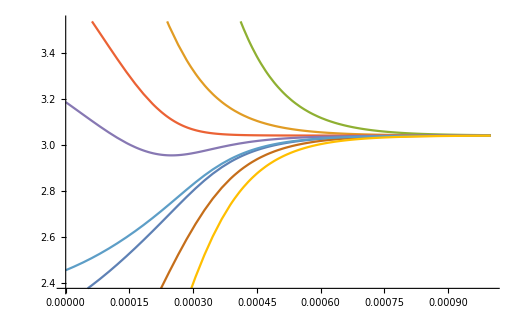

```mathematica
Plot[{oo1[t],oo2[t],oo3[t],oo4[t],oo5[t],oo6[t],oo7[t],oo8[t]},{t,0,0.001}]
```